```mathematica
k=8.31451070*10^-3;
m=18.0153;
h=0.3990313224;
sym=2;
ThAThBThC=(h^2/(8Pi^2k))^3/(0.00614517*0.01155002*0.01769519)
```

11360.3

```mathematica
densityF =SparseArray[{300->.98,360->.96,420->.93,480->.9}];
```

```mathematica
len=10;
dt=0.004;
```

```mathematica
S[T_,nMol_, file_,rho_]:=Module[{c1, Ct,gT,j,h1,De,f1,f,gg,Dw,gs,Sig,fy,z,SHs,Wgs,hb,beta,Who,Svib,Sconf,Srot},c1=k*T*3 *nMol; Ct=Import[file,"Table"] ; Ct[[All,2]]=Ct[[All,2]]*c1;gT=2/k /T*dt*(Chop[Fourier[Ct[[All,2]],FourierParameters->{1,1}]+Fourier[Ct[[All,2]],FourierParameters->{1,-1}] - Ct[[1,2]]]);j[f_,y_]:=2*y^3*f^3-(y+6y^2)*f^2+(2+6y)*f-2;h1[f_,D_]:=j[f,(f/D)^(3/2)];De=2*gT[[1]]/9/nMol*(Pi*k*T/m)^(1/2)*rho^(1/3)*(6/Pi)^(2/3);f1=f/.ToRules[Reduce[h1[f,De]==0,f,Reals]];gg[w_]:=gT[[1]]/(1+(gT[[1]]*w/(12*f1*nMol))^2);Dw=2*Pi/len;gs[w_]:=gT[[1+w/Dw]]-gg[w];Sig= k*(Log[1/rho*(4*Pi*m*3/2*nMol*k*T/(3*nMol*h^2))^(3/2)]+5/2);z[y_]:=(1+y+y^2-y^3)/(1-y)^3;fy=f1*(f1/De)^(3/2);SHs=Sig+k*(Log[z[fy]]+fy*(3*fy-4)/(1-fy)^2);Wgs=1/3*SHs/k;hb=h/2/Pi;beta=1/k/T;Who[w_]:=beta*hb*w/(Exp[beta*hb*w]-1)-Log[1-Exp[-beta*hb*w]];Svib=k*Sum[Dw/2/Pi*gs[w]*Who[w],{w,Dw,1/dt*Pi,Dw}];Sconf=k*Sum[Dw/2/Pi*gg[w]*Wgs,{w,0,1/dt*Pi,Dw}];
(Svib+Sconf)/nMol*1000]
```

```mathematica
Srot[T_,nMol_, file_,rho_]:=Module[{c1, Ct,gT,j,h1,De,f1,f,gg,Dw,gs,Sig,fy,z,SR,Wgs,hb,beta,Who,Svib,Sconf,Srot},c1=k*T*3 *nMol; Ct=Import[file,"Table"] ; Ct[[All,2]]=Ct[[All,2]]*c1;gT=2/k /T*dt*(Chop[Fourier[Ct[[All,2]],FourierParameters->{1,1}]+Fourier[Ct[[All,2]],FourierParameters->{1,-1}] - Ct[[1,2]]]);j[f_,y_]:=2*y^3*f^3-(y+6y^2)*f^2+(2+6y)*f-2;h1[f_,D_]:=j[f,(f/D)^(3/2)];De=2*gT[[1]]/9/nMol*(Pi*k*T/m)^(1/2)*rho^(1/3)*(6/Pi)^(2/3);f1=f/.ToRules[Reduce[h1[f,De]==0,f,Reals]];gg[w_]:=gT[[1]]/(1+(gT[[1]]*w/(12*f1*nMol))^2);Dw=2*Pi/len;gs[w_]:=gT[[1+w/Dw]]-gg[w];Sig= k*(Log[1/rho*(4*Pi*m*3/2*nMol*k*T/(3*nMol*h^2))^(3/2)]+5/2);z[y_]:=(1+y+y^2-y^3)/(1-y)^3;fy=f1*(f1/De)^(3/2);SR=Log[Pi^(1/2)*E ^(3/2)/sym*(T^3/ThAThBThC)^(1/2)]*k; Wgs=1/3*SR/k;hb=h/2/Pi;beta=1/k/T;Who[w_]:=beta*hb*w/(Exp[beta*hb*w]-1)-Log[1-Exp[-beta*hb*w]];Svib=k*Sum[Dw/2/Pi*gs[w]*Who[w],{w,Dw,1/dt*Pi,Dw}];Sconf=k*Sum[Dw/2/Pi*gg[w]*Wgs,{w,0,1/dt*Pi,Dw}];
(Svib+Sconf)/nMol*1000]
```

```mathematica
nMol=988;dir="c:\\Users\\rschulz\\Documents\\work\\lignin_entropie\\water\\";
```

```mathematica
For[T=300,T≤480,T+=60, l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];S[T,nMol,dir<>"vac"<>fn<>".cvs",nMol/Import[dir<>"vol"<>fn<>".dat","Table"][[1,2]]]],Range[0,80,20]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]]];
```

300 54.3785 0.187403

360 63.2357 0.0884352

420 70.4708 0.0793841

480 77.781 0.171635

```mathematica
(*new data*)
```

```mathematica
For[T=300,T≤480,T+=60, l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];S[T,nMol,dir<>"corr"<>fn<>".dat",nMol/Import[dir<>"vol"<>fn<>".dat","Table"][[1,2]]]],Range[0,80,20]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]]];
```

300 54.4175 0.190288

360 63.2237 0.206644

420 70.5805 0.181005

480 77.8311 0.187842

```mathematica
For[T=300,T≤480,T+=60, l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];Srot[T,nMol,dir<>"rot"<>fn<>".dat",nMol/Import[dir<>"vol"<>fn<>".dat","Table"][[1,2]]]],Range[0,80,20]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]]];
```

300 13.1723 0.0280742

360 18.3848 0.0397038

420 23.4987 0.106856

480 28.6772 0.134925

```mathematica
nMol=988;dir="c:\\Users\\rschulz\\Documents\\work\\lignin_entropie\\water\\";
Map[Function[T,T->densityF[[T]]*nMol/Mean[Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];Import[dir<>"vol"<>fn<>".dat","Table"][[1,2]]],Range[0,80,20]]]],Range[300,480,60]]
density=SparseArray[%];
```

{300→32.043,360→29.4605,420→26.0182,480→21.7589}

```mathematica
(*old data - difference to bulk water)
```

```mathematica
dir="c:\\Users\\rschulz\\Documents\\work\\lignin_entropie\\";
```

```mathematica
For[T=300,T≤300,T+=60, Do[l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];
nMol=Import[dir<>"size"<>fn<>".dat","Table"][[1,2]]/3;(54.3785-S[T,nMol,dir<>"vac"<>fn<>".cvs",density[[T]]])*nMol],Range[p,p+2]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]],{p,{1,4}}]];  (*p is the starting number of the files for one temp - to average seperate e.g. over collapsed/extended*)
```

300 1170.82 52.0112

300 1206.59 63.289

```mathematica
(*new data - difference to bulk water)
```

```mathematica
For[T=300,T≤300,T+=60, Do[l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];
nMol=Import[dir<>"size"<>fn<>".dat","Table"][[1,2]]/3;(54.4175-S[T,nMol,dir<>"corr"<>fn<>".dat",density[[T]]])*nMol],Range[p,p+2]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]],{p,{1,4}}]];
```

300 1109.84 61.0493

300 1349.98 104.095

```mathematica
(*old data - absolute value)
```

```mathematica
For[T=300,T≤300,T+=60, Do[l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];
nMol=Import[dir<>"size"<>fn<>".dat","Table"][[1,2]]/3;(S[T,nMol,dir<>"vac"<>fn<>".cvs",density[[T]]])],Range[p,p+2]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]],{p,{1,4}}]];
```

300 52.5074 0.104896

300 52.7171 0.0619765

```mathematica
(*new data - absolute value)
```

```mathematica
For[T=300,T≤300,T+=60, Do[l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];
nMol=Import[dir<>"size"<>fn<>".dat","Table"][[1,2]]/3;(S[T,nMol,dir<>"corr"<>fn<>".dat",density[[T]]])],Range[p,p+2]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]],{p,{1,4}}]];
```

300 52.6447 0.0926025

300 52.5484 0.266077

```mathematica
(*rotational - missing correct rotational momentum*)
For[T=300,T≤300,T+=60, Do[l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];
nMol=Import[dir<>"size"<>fn<>".dat","Table"][[1,2]]/3;(Srot[T,nMol,dir<>"rot"<>fn<>".dat",density[[T]]])],Range[p,p+2]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]],{p,{1,4}}]];
```

300 13.1695 0.0291565

300 13.0844 0.0214523

```mathematica
For[T=300,T≤300,T+=60, Do[l=Map[Function[i,fn=ToString[T]<>"_"<>ToString[i];
nMol=Import[dir<>"size"<>fn<>".dat","Table"][[1,2]]/3;(13.1723-Srot[T,nMol,dir<>"rot"<>fn<>".dat",density[[T]]])*nMol],Range[p,p+2]];Print[ToString[T]<>" " <>ToString[Mean[l]]<>" " <>ToString[StandardDeviation[l]]],{p,{1,4}}]];
```

300 1.44652 18.1918

300 63.1051 10.7848

```mathematica
S[300,637,dir<>"vac300_1.cvs",density[[300]]]
```

1000/637 (-0.239464+0.00831451 (0.444223 (-0.00320724+(0.00320724 (Fourier[Symbol[],FourierParameters→{1,-1}]+Fourier[Symbol[],FourierParameters→{1,1}]-$Failed⟦1,2⟧))⟦3⟧)+«1249»))

```mathematica
S[300,637,dir<>"corr300_1.dat",density[[300]]]
```

52.7519

```mathematica
Srot[300,637,dir<>"rot300_1.dat",density[[300]]]
```

13.2097

```mathematica
Plot[-39255.6-T*-39255.6,T]
```

Plot::pllim: Range specification T is not of the form {x, xmin, xmax}.

Plot[-39255.6-T (-39255.6),T]

```mathematica
Plot[-39255.6-T (-39255.6),T,300,480]
```

Plot::nonopt: Options expected (instead of 480) beyond position 2 in Plot[-39255.6 - T\ (-39255.6), T, 300, 480]. An option must be a rule or a list of rules.

Plot[-39255.6-T (-39255.6),T,300,480]

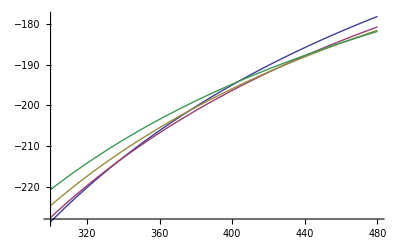

```mathematica
Plot[{(-39255.6+3/4*nMol*k*(T-300)-T 97.8589)/T,(-36087.5+3/4*nMol*k*(T-360)-T*106.515)/T,(-32818.5+3/4*nMol*k*(T-420)-T*113.627)/T,(-29189.6+3/4*nMol*k*(T-480)-T*120.95)/T},{T,300,480}]
```